# Covid - 19 on Cruise Lines

Math 9 Final Project
Fall 2020
By Austin Zhong

I’d like to give a little preface on why I chose my topic to be about Covid-19’s affect on cruise lines. As we all know, traveling puts people at a high risk for contracting and spreading the virus. Airplane travel was the first to come to my mind, but there was an industry that was hit even harder than airlines. Cruises, a perfect storm for mass incubation and spread of Covid-19. Imagine an isolated ship, filled with thousands of people, with limited space, supplies, and professionals battling the highly contagious virus. It’s with reasonable intuition that the CDC issued a No Sail Order and Conditional Sailing Order effective from March 2020 to November 2021. I’d like to explore the effects of Covid-19 on cruise stocks and create a model simulating the spread of Covid-19 on a full capacity cruise liner.

```mathematica
(*https://www.cdc.gov/quarantine/cruise/index.html*)
```

```mathematica
(*I started working on cruise line stocks because that seemed like the most tangable thing I could display and analyze. Thankfully Mathmatica makes it easy to access stock data. It took me a little bit to get used to working with entities.*)
```

```mathematica
(*https://reference.wolfram.com/language/ref/FinancialData.html*)
clStocks[x_]:=DateListPlot[FinancialData[x,LinguisticAssistant],PlotRange->{0,140},PlotStyle->RandomColor[1],PlotLegends->LineLegend[{x}]]
```

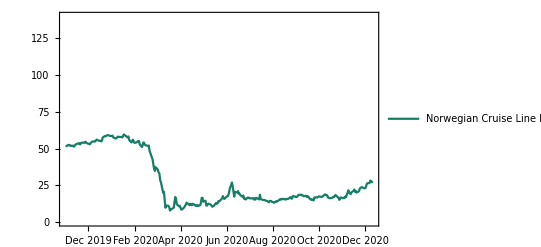

```mathematica
p1=clStocks[Entity["Financial","NASDAQ:NCLH"]]
```

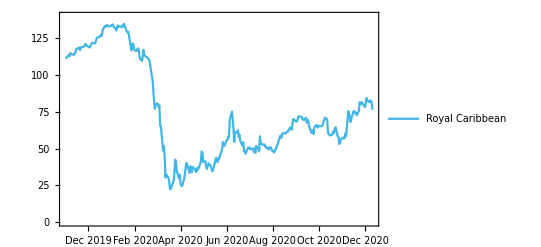

```mathematica
p2=clStocks[Entity["Financial","NYSE:RCL"]]
```

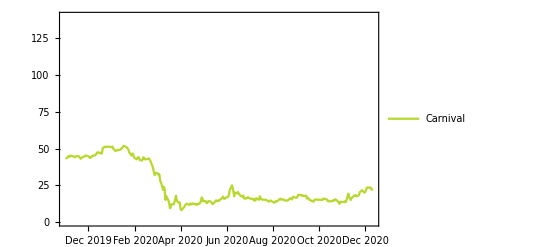

```mathematica
p3=clStocks[Entity["Financial","NYSE:CCL"]]
```

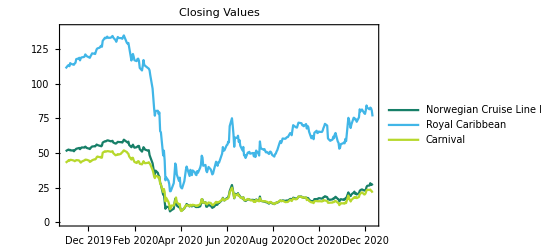

```mathematica
Show[p1,p2,p3,PlotLabel->"Closing Values"]
```

```mathematica
(*DONE*)(*Graph looks okay, but I want there to be a legend for each stock*)
```

```mathematica
(*DONE*)(*Figure out way to find closing values at specific dates to find percentage loss and compare*)(*Something new I learned was TimeSeries. TimeSeries made it nice to find stock values at any given date*)
```

```mathematica
(*I tried making a function that could automate this process of finding stock values of two given dates for 3 of the Cruise Lines. Might need to look into it again, for now this will do.*)
```

```mathematica
Clear[clPrice]
Clear[ts]
clPrice[x_]:=ts:=FinancialData[x,LinguisticAssistant]
clPrice[Entity["Financial","NYSE:RCL"]]
precov=ts["January 1, 2020"]
postcov=ts["April 1, 2020"]
percent1=(precov-postcov)/precov
```

134.08 $

25.77 $

0.807801

```mathematica
Clear[clPrice]
Clear[ts]
clPrice[x_]:=ts:=FinancialData[x,LinguisticAssistant]
clPrice[Entity["Financial","NYSE:CCL"]]
precov=ts["January 1, 2020"]
postcov=ts["April 1, 2020"]
percent2=(precov-postcov)/precov
```

51.07 $

8.80 $

0.827687

```mathematica
Clear[clPrice]
Clear[ts]
clPrice[x_]:=ts:=FinancialData[x,LinguisticAssistant]
clPrice[Entity["Financial","NASDAQ:NCLH"]]
precov=ts["January 1, 2020"]
postcov=ts["April 1, 2020"]
percent3=(precov-postcov)/precov
```

58.62 $

9.55 $

0.837086

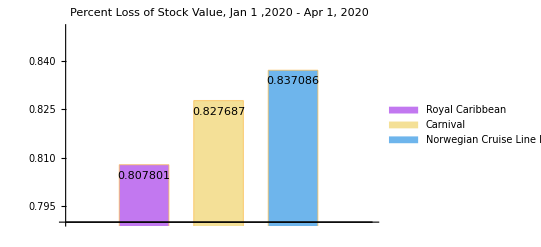

```mathematica
(*https://reference.wolfram.com/language/ref/ChartLabels.html*)
BarChart[{percent1,percent2,percent3},BarSpacing->Large,PlotRange->{Automatic,{0.79,0.85}},ChartStyle->{"Pastel"},ChartLabels->{Placed[{percent1,percent2,percent3},Top]},ChartLegends->{"Royal Caribbean","Carnival","Norwegian Cruise Line Holdings"},PlotLabel->"Percent Loss of Stock Value, Jan 1 ,2020 - Apr 1, 2020"]
```

```mathematica
(*task*)
(*Find NonLinearModelFit of stocks starting from April 1, 2020*)(*this would give a hypothetical estimate on when stock values would return to precov values*)(*I think this is going to be difficult due to TimeSeries. I'm not sure I can extend the x-axis timeline in order to predict future values*)
```

```mathematica
p2
```

-Graphics-

```mathematica
(*Here, I just wanted to cut the graph so I could work on the linear fit model more easily*)
```

```mathematica
aprStocks[x_]:=DateListPlot[FinancialData[x,LinguisticAssistant],PlotRange->{0,140},PlotStyle->RandomColor[1],PlotLegends->LineLegend[{x}]]
```

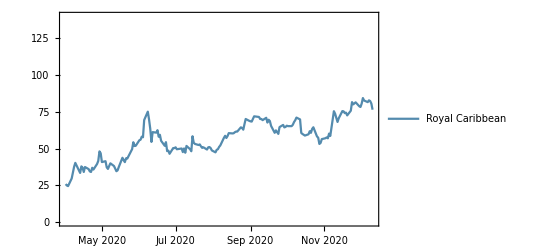

```mathematica
rc=aprStocks[Entity["Financial","NYSE:RCL"]]
```

```mathematica
(*UPDATE*)
(*Mathmatica does it again. I found a simple way to forecast stock prices here: https://www.wolfram.com/mathematica/new-in-10/time-series/build-a-model-for-forecasting-stock-prices.html*)
```

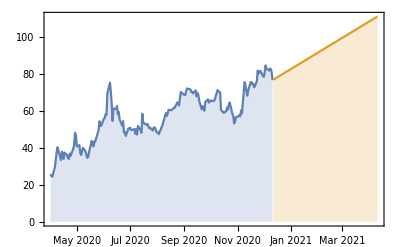

```mathematica
rcfd=FinancialData[Entity["Financial","NYSE:RCL"],LinguisticAssistant];
rcfit=TimeSeriesModelFit[rcfd];
forec=TimeSeriesForecast[rcfit,{120}];
DateListPlot[{rcfd,forec},Filling->Axis]
```

```mathematica
(*Below I have a series of functions that take in the string of the 3 cruise line financial identities so I don't have to copy and paste the code I have above for each of the 3 entities*)
```

```mathematica
string={LinguisticAssistant,Entity["Financial","NYSE:CCL"],Entity["Financial","NASDAQ:NCLH"]}
```

{Royal Caribbean,Carnival,Norwegian Cruise Line Holdings}

{TimeSeriesModel[…],TimeSeriesModel[…],TimeSeriesModel[…]}

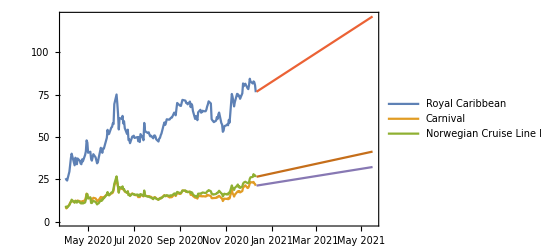

```mathematica
financial[x_]:=FinancialData[x,LinguisticAssistant]
z=financial[string];
function[x_]:=TimeSeriesModelFit[financial[x]]
tsmstring=function/@string
for=Table[TimeSeriesForecast[tsmstring[[i]],{156}],{i,1,Length[string]}];
(*156 weeks (3 years) is roughly when Royal Caribbean stocks will rise back to it's pre-covid value. I'm not sure if it would be a good use of my time to write a program that could automatically give me a date if I were to input some closing value*)
DateListPlot[{z,for},PlotLegends->string]
```

```mathematica
(*I noticed one of the forcasts was non-linear and double-checked it to be the Carnival forcast*)
(*UPDATE*)
(*The Carnival forecast is no longer in the SARIMA family. I'm not sure what happened, I just re-evaluated the notebook*)
```

TimeSeriesModel[…]

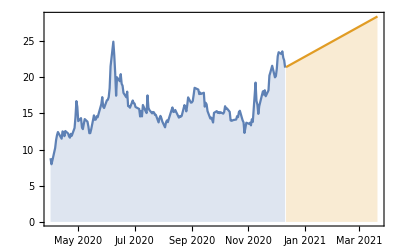

```mathematica
cfd=FinancialData[Entity["Financial","NYSE:CCL"],LinguisticAssistant];
cfit=TimeSeriesModelFit[cfd]
for=TimeSeriesForecast[cfit,{100}];
DateListPlot[{cfd,for},Filling->Axis]
```

```mathematica
(*Here marks a revamp of my code and figures which I have displayed above*)
(*A website was used to import ticker symbols of cruise line and travel  stocks*)
reglist=Import["https://swingtradebot.com/stocks-tagged-as/12139-cruise-lines","Data"];
```

```mathematica
Position[reglist,x_String/;StringContainsQ[x,"AGYS"]]
```

{{2,1,2,2,1,1},{2,1,4,2,1,2},{2,1,4,2,2,2}}

```mathematica
Position[reglist,x_String/;StringContainsQ[x,"NCLH"]]
```

{{2,1,2,2,3,1},{2,1,4,2,15,2},{2,1,4,2,16,2}}

```mathematica
(*Both symbols show up in {2,1,2,2}*)
```

```mathematica
name=Extract[reglist,{2,1,2,2}]
```

{{ AGYS , Agilysys, Inc. },{ EXPE , Expedia, Inc. },{ NCLH , Norwegian Cruise Line Holdings Ltd. },{ TZOO , Travelzoo Inc. },{ CCL , Carnival Corporation },{ CUK , Carnival Plc ADS ADS },{ EVI , EnviroStar, Inc. },{ INT , World Fuel Services Corporation },{ RCL , Royal Caribbean Cruises Ltd. },{ SABR , Sabre Corporation },{ LIND , Lindblad Expeditions Holdings Inc. }}

```mathematica
symblist=Table[StringTrim[x[[1]]],{x,name}]
```

{AGYS,EXPE,NCLH,TZOO,CCL,CUK,EVI,INT,RCL,SABR,LIND}

```mathematica
(*I wanted to turn my list of strings into a list of entities*)
entfunc[x_]:=Interpreter["Financial"][x]
entlist=entfunc/@symblist
```

{Agilysys,Expedia,Norwegian Cruise Line Holdings,Travelzoo,Carnival,Carnival,Failure[…],World Fuel,Royal Caribbean,Sabre Corp,Failure[…]}

```mathematica
(*Weird. Mathmatica cannot access the financial data of EVI Industries and Lindblad Expeditions Holdings Inc*)
(*Mathmatica even failed to access the entity of EVI*)
LinguisticAssistant
Interpreter["Financial"]["Lindblad Expeditions Holdings Inc"]
```

Failure[…]

Failure[…]

```mathematica
(*I couldn't figure out why so I just deleted the failures from the list*)
(*https://resources.wolframcloud.com/FunctionRepository/resources/DeleteFailures*)
entlistfinal=ResourceFunction["DeleteFailures"][entlist]
```

{Agilysys,Expedia,Norwegian Cruise Line Holdings,Travelzoo,Carnival,Carnival,World Fuel,Royal Caribbean,Sabre Corp}

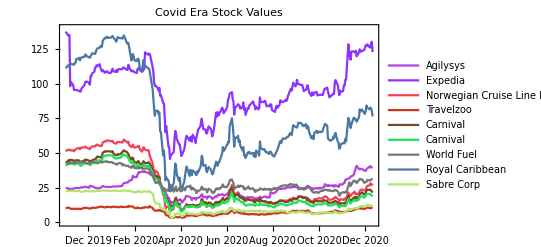

```mathematica
(*I made a function that takes the entity list and creates a graph for each companies' financial data*)
Clear[clstocks]
Clear[listgraph]
clstocks[x_]:=DateListPlot[FinancialData[x,LinguisticAssistant],PlotStyle->RandomColor[1],PlotRange->{0,140},PlotLegends->LineLegend[{x}],PlotLabel->"Covid Era Stock Values"]
listgraph=clstocks/@entlistfinal;
Show[listgraph]
```

```mathematica
(*Now that I have my beefed up stocks graph, I will now remake the percent loss bar chart with my new companies*)
(*Starting with my function*)
clPrice[x_]:=(ts=FinancialData[x,LinguisticAssistant];
precov=ts["January 1, 2020"];
postcov=ts["April 1, 2020"];
percent2=(precov-postcov)/precov)
percentList=clPrice/@symblist
```

{0.392815,0.525374,0.837086,0.637368,0.827687,0.831248,0.455944,0.484124,0.807801,0.780482,0.773237}

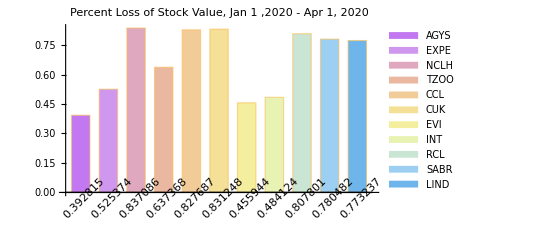

```mathematica
BarChart[percentList,BarSpacing->Large,ChartStyle->{"Pastel"},ChartLegends->{symblist},ChartLabels->Placed[percentList,Axis,Rotate[#,Pi/4]&],PlotLabel->"Percent Loss of Stock Value, Jan 1 ,2020 - Apr 1, 2020"]
```

```mathematica
(*^Here^, I accidentally used symblist instead of entlistfinal. I realized I was able to access the financial data without the use of entities so I tried it with my clstocks function*)
```

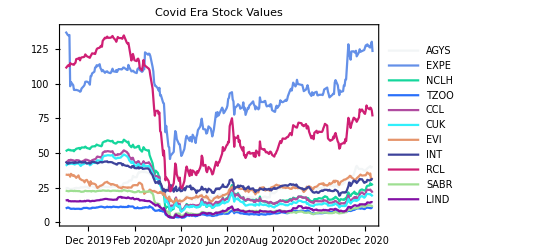

```mathematica
fingraph=clstocks/@symblist;
Show[fingraph]
```

```mathematica
(*It worked! EVI and LIND are here now*)
```

```mathematica
(*Created a GIF to see individual graphs more clearly*) 
stockgif=ListAnimate[fingraph]
```

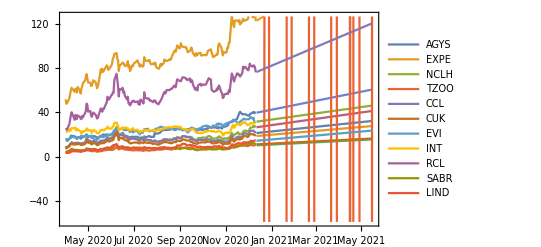

```mathematica
(*Now I will apply my new symblist to my stock forcast function*)
p=symblist;
financial[x_]:=FinancialData[x,LinguisticAssistant]
z=financial[p];
function[x_]:=TimeSeriesModelFit[financial[x]]
tsmstring=function/@p;
for=Table[TimeSeriesForecast[tsmstring[[i]],{156}],{i,1,Length[p]}];
forlist=DateListPlot[{z,for},PlotLegends->p]
```

```mathematica
(*I realize now that my code was not robust enough for me to create a GIF. I needed to get a string of forecasts*)
```

```mathematica
(*Here I redo my code above, with the intention of only inputting symblist once, and being able to create a GIF from the result*)
```

```mathematica
Clear[financial]
Clear[stocks]
financial[x_]:=FinancialData[x,LinguisticAssistant]
(*stocks is my first important list for DateListPlot*)
stocks=financial/@symblist;
```

```mathematica
Clear[eproc]
Clear[forecast]
Clear[forecastlist]
eproc=TimeSeriesModelFit/@stocks;
forecast[x_]:=TimeSeriesForecast[x,{156}] (*156(weeks) shows up again because I want to forecast the next 3 years*)
(*forecastlist is my second important list*)
forcastlist=forecast/@eproc;
```

```mathematica
(*Iterating both lists in one table gives me the list of stock forecasts I need*)
Clear[graphlist]
graphlist=Table[DateListPlot[{stocks[[i]],forcastlist[[i]]},PlotLegends->symblist[[i]],PlotStyle->ColorData["Rainbow"][i/10],PlotLabel->"3-year Stock Forecast"],{i,1,Length[stocks]}];
```

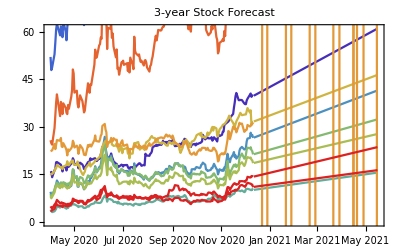

```mathematica
Show[graphlist]
```

```mathematica
(*GIF to show graphs individually*)
forecgif=ListAnimate[graphlist]
```

```mathematica
stockgif
```

```mathematica
(*Comparing the two GIFs allow us to see if the companies can recover from the crash after 3 years*)
```

```mathematica
(*Here I begin my attempt to model the spread of Covid-19 within a population*)
(*The main goal here is to apply the model to an imaginary cruise line passenger population and observe how long it takes for the whole population to become infected/deceased*)
(*This is pretty dark, so emphasis on imaginary*)
```

```mathematica
(*https://covidtracking.com/data/download*)
(*https://reference.wolfram.com/language/ref/Drop.html*)
SetDirectory["C:\\Users\\Austin Zhong\\Documents\\Wolfram Mathematica"];
nat=Reverse[Import["national-history.csv","Dataset",HeaderLines->1]];
natdat=nat[All,{"date","death","positive"}];
natdat1=Drop[natdat,34];
natdat2=Drop[natdat1,{40,Length[natdat1]}]
(*For my use, dates weren't needed so I replaced that column with a day column*)
days=Table[i,{i,1,Length[natdat2]}];
day=Table[Association["day"->days[[i]]],{i,1,Length[days]}];
daycol=Dataset[day]
daydat=Join[natdat2,daycol,2]
findat=daydat[All,{"day","death","positive"}]
```

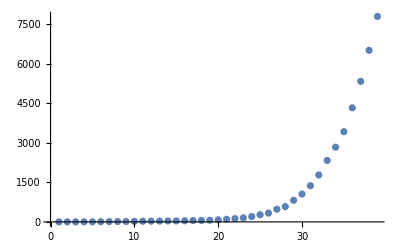

```mathematica
(*Citation:Wednesday office hour with Deborah*)
xVal=Normal[findat[All,"day"]];
yVal=Normal[findat[All,"death"]];
y2Val=Normal[findat[All,"positive"]];
deathdat=Transpose[{xVal,yVal}];
dplot=ListPlot[deathdat]
```

```mathematica
(*This model gives me the amount of deaths for a given period of days*)
```

```mathematica
model=a*b^(x)+d
fit=FindFit[deathdat,model,{a,b,d},x]
fn[x_]:=Evaluate[model/.fit]
fn[30]
```

a b^x+d

{a→2.01819,b→1.23683,d→-40.2221}

1146.37

```mathematica
(*1146.37 deaths is a resonable prediction after 30 days*)
(*Plot best fit line with points to double check the fit*)
```

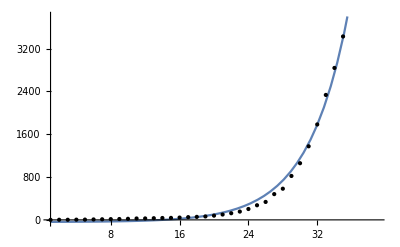

```mathematica
Plot[Evaluate[model/.fit],{x,Min[xVal],Max[xVal]},Epilog->Map[Point,deathdat]]
```

4.70467 Log[0.495493 (40.2221+x)]

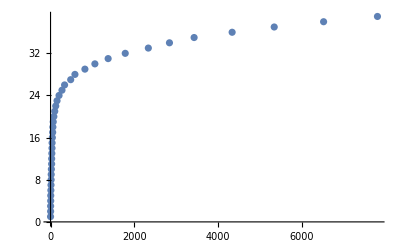

30.

```mathematica
(*I'd like to have my model read a population/death value and then give me a day value so I created a new plot with deaths on the x-axis and days on the y-axis*)

model2=Log[b,(x-d)/a]/.{a->2.0181922245053827,b->1.2368337535865384,d->-40.22205912362602}
deathdat2=Transpose[{yVal,xVal}];
dplot2=ListPlot[deathdat2]
deaths[x_]:=Evaluate[model2/.fit]
deaths[1146.3726068518808]
```

```mathematica
dbestfit=Plot[model2/.{a->2.0181922245053827,b->1.2368337535865384,d->-40.22205912362602},{x,1,6000}];
```

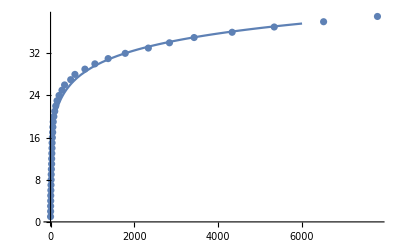

```mathematica
Show[dplot2, dbestfit]
```

```mathematica
(*model2 looks good*)
```

```mathematica
(*Now do the same for positive cases*)
```

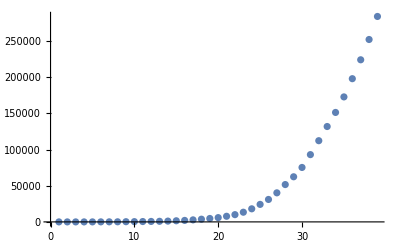

```mathematica
xValue=Normal[findat[All,"day"]];
yValue=Normal[findat[All,"positive"]];
y2Value=Normal[findat[All,"positive"]];
posdat=Transpose[{xValue,yValue}];
pplot=ListPlot[posdat]
```

```mathematica
model=a*b^(x)+d;
posfit=FindFit[posdat,model,{a,b,d},x];
fn[x_]:=Evaluate[model/.posfit]
fn[30]
```

75709.1

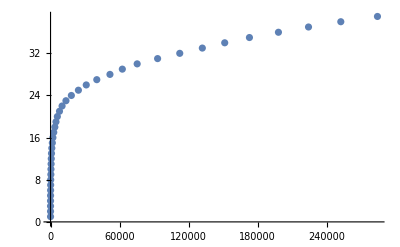

```mathematica
invposdat=Transpose[{yValue,xValue}];
invpplot=ListPlot[invposdat]
```

```mathematica
model3=Log[b,(x-d)/a]/.{a->1072.1330583014733,b->1.1558848810752995,d->-7025.274203379352};
positive[x_]:=Evaluate[model3/.posfit]
positive[75709.13763120372]
(*Cross refrence previous x y values to double check models*)
```

30.

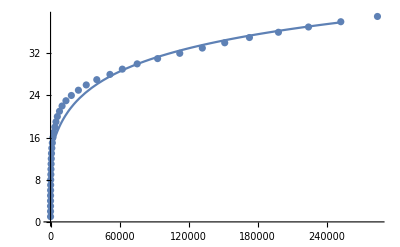

```mathematica
pbestfit=Plot[model3/.{a->1072.1330583014733,b->1.1558848810752995,d->-7025.274203379352},{x,1,250000}];
Show[invpplot,pbestfit]
```

```mathematica
(*Now with my deaths and positive functions, I can estimate the value of deaths and poisitve cases for any given population*)
```

```mathematica
(*https://www.businessinsider.com/royal-caribbean-debuts-worlds-largest-cruise-ship-photos-2018-4*)
(*The Symphony of the Seas is the largest passenger capacity cruise ship, holding up to 6680 passengers*)
(*Let's see what happens when Covid-19 is added to the mix >:)*)
positive[6680]
```

17.5895

```mathematica
(*In roughly 17 days, the Symphony of Seas will become the Symphony of Positive Covid-19 Cases*)
```

```mathematica
deaths[6680]
```

38.1581

```mathematica
(*In roughly 38 days, the Symphony of Seas will become the world's largest floating graveyard*)
```

The End

Epilogue:
I would’ve liked to dive deeper into my deaths and positive predictions using imported datasets of cruise ship passengers, but I feel I have done sufficient work accounting for the whole of my project. Working on the project and getting a chunk of code right granted me one of the most rewarding feelings, the type of feeling that makes you get up and dance. I learned a lot about the capabilities of Mathematica from this project alone, and I am incredibly proud of what I have accomplished.  Thank you Professor Davis and Deborah for facilitating my learning. It was a pleasure attending the class.